# Microwave + RF state mapping

P. Huft

## Setup

```mathematica
(*get from local files*)
SetDirectory[NotebookDirectory[]];
<<"../constants/rbconsts.m"
<<"../constants/physconsts.m"
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 14],ImageSize->Medium];
SetOptions[ListPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 14],ImageSize->Medium];
SetOptions[ListLogPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 14],ImageSize->Medium];
SetOptions[ListLogLogPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 14],ImageSize->Medium];
EHFeV = JToeV[EHF]; 
GHzToJ[ν_]:=10^9 h ν;
GHzToeV[ν_]:=(10^9 h ν)/e ;
JToGHz[u_]:=u/(10^9 h);
JToMHz[u_]:=u/(10^6 h);
JToeV[u_]:=u/e;
eVToGHz[u_]:=e/(10^9 h)u;
KetForm[{F_,m_}]:=F,m; 
(*define some units in terms of the standard SI units*)
GHz=10^9;
MHz=10^6;
kHz=10^3;
G=10^-4;
```

## Two-photon microwave + RF transition

-Graphics-

```mathematica
(*double letter labels for the upper state quantum numbers*)
HFZ1MatElem[I_,J_,gJ_,{F_,mF_},{FF_,mFF_},Bz_]:=Quiet[μB Bz (ClebschGordan[{F,mF},{1,0},{FF,mFF}] √(2 F +1)(-1)^(1+J+I)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,I,F},{FF,1,J}]+
gI(-1)^FF √(I(I+1)(2I+1))SixJSymbol[{I,J,F},{FF,1,I}]))];
KetForm[{F_,m_}]:=F,m;(*for printing nice labels*)
```

```mathematica
Clear[gF]
S = 1/2; 
L = 0; 
J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF[F_]:= (gJ(F(F+1)+J(J+1)-INuc(INuc+1))
+gI(F(F+1)-J(J+1)+INuc(INuc+1)))/(2F(F+1));
states = Flatten[Table[Table[{F,mF},{mF,-F,F}],{F,{2,1}}],1];
"g_(F = 1):"
gF[1]
"g_(F = 2):"
gF[2]
```

g_(F = 1):

-0.501301

g_(F = 2):

0.499311

Compute Hamiltonians in eV to avoid ridiculously small numbers

```mathematica
dim = Length[states];
HZ1[Bz_]=Table[Table[JToeV[HFZ1MatElem[INuc,J,gJ,states[[i]],states[[j]],Bz]],{i,1,dim}],{j,1,dim}];
HAtom = Array[0&,{8,8}];
Array[(HAtom[[#,#]]=EHFeV)&,5];
HTotal[B_]=HAtom + HZ1[B];
ZShifts[B_]=SortBy[Eigenvalues[HTotal[B]],#/.B->0.1&];(*Eigenenergies [eV]*)
BList = Range[0,0.5,.1];
```

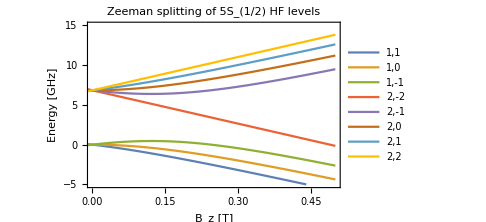

```mathematica
Bmax = 0.5; (*[T]*)
Plot[Evaluate[eVToGHz[ZShifts[B]]],{B,-Bmax,Bmax},PlotRange->{{0,Bmax},{-5,15}},PlotLabel->"Zeeman splitting of 5S_(1/2) HF levels ",FrameLabel->{"B_z [T]","Energy [GHz]"},PlotLegends->LineLegend[Join[Reverse[Array[KetForm[states[[#+5]]]&,3]],Array[KetForm[states[[#]]]&,5]],LabelStyle->Directive[Black,FontSize->10]]]
```

```mathematica
Join[Reverse[Array[KetForm[states[[#+5]]]&,3]],Array[KetForm[states[[#]]]&,5]]
```

{1,1,1,0,1,-1,2,-2,2,-1,2,0,2,1,2,2}

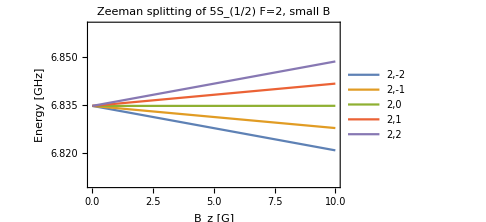

```mathematica
Bmax=10;
Plot[Evaluate[eVToGHz[ZShifts[B*10^-4][[4;;]]]],{B,0,Bmax},PlotRange->{{0,Bmax},{6.81,6.86}},PlotLabel->"Zeeman splitting of 5S_(1/2) F=2, small B",FrameLabel->{"B_z [G]","Energy [GHz]"},PlotLegends->LineLegend[Array[KetForm[states[[#]]]&,5],LabelStyle->Directive[Black,FontSize->10]]]
```

```mathematica
"MHz/G"
μB gF[2] G/(h 10^6)
```

MHz/G

0.698878

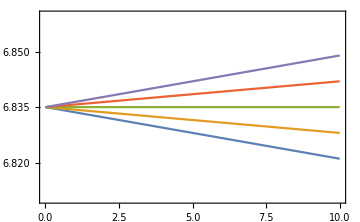

```mathematica
Plot[Evaluate[Table[μB gF[2] B G m/(h 10^9)+6.835,{m,{-2,-1,0,1,2}}]],{B,0,Bmax},PlotRange->{6.81,6.86}]
```

```mathematica
FiveSOneHalfShiftsGHz[B_]=eVToGHz[ZShifts[B]];
```

```mathematica
(c/(780*10^-9)-c/(790*10^-9))
```

4.86644×10^12

```mathematica
(c/(780*10^-9)-c/(795*10^-9))
```

7.25375×10^12